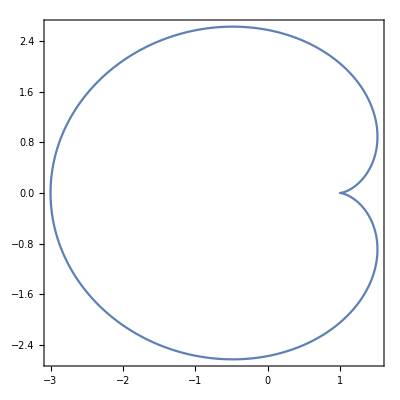

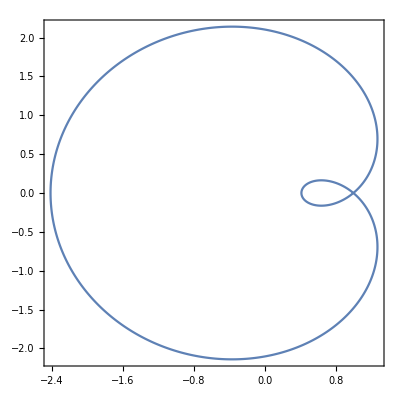

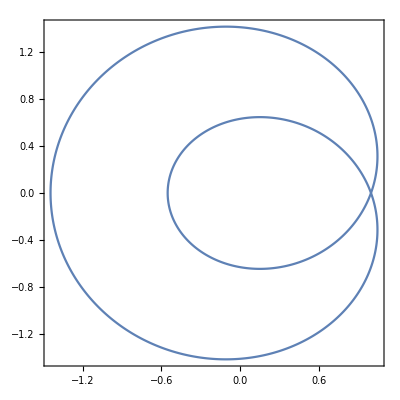

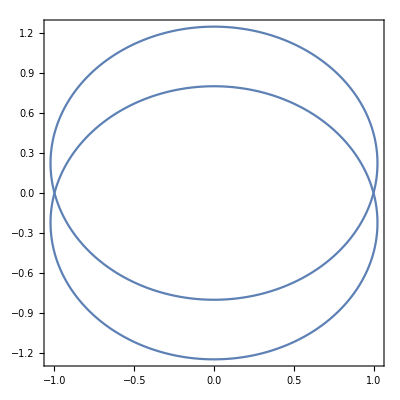

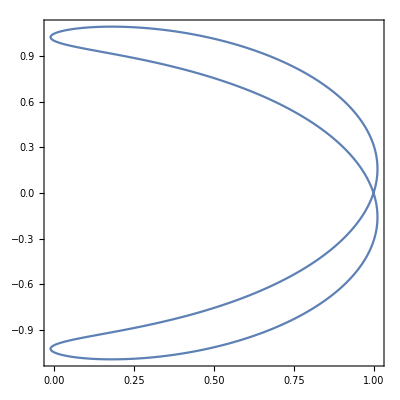

-Graphics-

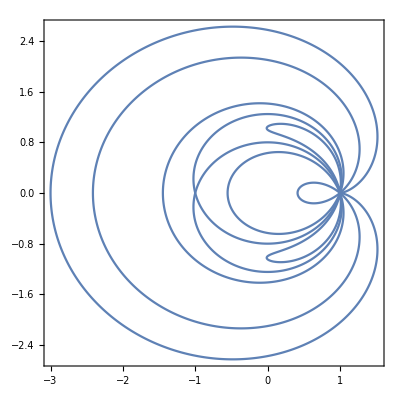

```mathematica
ClearAll[W,x,y]
γ = 1/10;
H[x_,y_,W_]=1/4*(x^2+y^2)^2-W/2*(x^2+y^2)-(1-W)*x-γ/2*y^2;
R[W_]:= RegionPlot[ImplicitRegion[H[x,y,W]==W/2-3/4,{{x,-10,10},{y,-10,10}}]];
R1 = R[3]
R2 = R[2]
R3 = R[1.1]
R4 = R[1]
R5 = R[0.95]
R6 = R[0.9]
Show[R1,R2,R3,R4,R5,R6]
```